1

√2

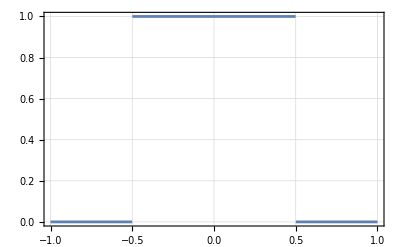

√2 ⅇ^(-1/2 d^2 k1^2)

```mathematica
delta = 0.5;
bump[x_,d_]:=(HeavisideTheta[x+d]-HeavisideTheta[x-d])/(2* d);
gaussianBump[x_,d_]:=Exp[-x^2/(2*d^2)]/(Sqrt[2*Pi]* d);
Integrate[bump[x,d],{x,-Infinity,Infinity}, Assumptions->d > 0]
Integrate[gaussianBump[x,d],{x,-Infinity,Infinity}, Assumptions->d > 0]


Plot[{bump[x,delta],gaussianBump[x,delta]},{x,-1,1}, Frame->True, GridLines->Automatic]
e[k_,z_,d_]:=Exp[I*k*z]*bump[z,d]

Integrate[Exp[-I*k1*x]*gaussianBump[x,d],{x,-Infinity,Infinity}, Assumptions->d > 0]
Integrate[Exp[-I*k1*x]*bump[x,d],{x,-Infinity,Infinity}, Assumptions->d > 0]
(* Integrate[Exp[I*k*x]*Exp[-I*k1*x]*bump[x,d],{x,-Infinity,Infinity}, Assumptions->d > 0] *)
(* Integrate[e[k,z,d]*Exp[-I*k1*z],{z,-Infinity, Infinity}, Assumptions->d > 0] *)
```

```mathematica
(* https://en.wikipedia.org/wiki/Gaussian_beam *)
k=2*Pi*n/λ
zR = Pi * w0^2 * n / λ 

R[z_]:=z*(1+(zR/z)^2);
w[z_]:=w0*Sqrt[1+(z/zR)^2];
ψ[z_]:=ArcTan[z/zR];

e[r_,z_]:=(w0/w[z])*Exp[-r^2/w[z]^2]*Exp[-I*(k*z+(k*r^2/(2*R[z]))-ψ[z])];
ea[r_,z_]:=e[r,z]*Exp[I*k*z]
e1[r_,z_]:=(w0/wz)*Exp[-r^2/wz^2]*Exp[-I*(k*z+(k*r^2/(2*Rz))-ψz)];

Print["w[z]^2/R[z]"]
FullSimplify[w[z]^2/R[z]]

Print["e[r,z]"]
e[r,z]
e[Sqrt[x^2+y^2],z]

Print["D[ea[r,z],z]"]
d1=FullSimplify[D[ea[r,z],z]]

Print["D[ea[r,z],{z,2}]"]
d2=FullSimplify[D[ea[r,z],{z,2}]]

Print["d2 /(k * d1)"]
d2d1=Simplify[FullSimplify[d2/ d1]/k]
z0Rule ={z -> 0};
zRRule ={z -> zR};
FullSimplify[d2d1 /. z0Rule]
FullSimplify[d2d1 /. zRRule]
Series[d2d1,{z, Infinity,2}]

(*
d2d1Nom=FullSimplify[(8 (w0^4 (z-ⅈ zR)^4 (z+ⅈ zR)^2+2 r^4 z^2 zR^4+r^2 w0^2 (z-ⅈ zR) (z+ⅈ zR) zR^2 ((-2+ⅈ) z+zR) ((2+ⅈ) z+zR))-k^2 w0^4 (r^2 (-z^2+zR^2)+2 (z^2+zR^2)^2)^2+4 ⅈ k w0^2 (2 w0^2 (z-ⅈ zR)^4 (z+ⅈ zR)^3+2 r^4 z (z-zR) zR^2 (z+zR)-r^2 (z^2+zR^2) (4 z zR^2 (z^2+zR^2)+w0^2 (2 z^3-ⅈ z^2 zR-4 z zR^2+ⅈ zR^3))))];

d2d1Denom=FullSimplify[((2 w0^2 (z^2+zR^2)^2 (-2 w0^2 (z-ⅈ zR)^2 (z+ⅈ zR)+4 r^2 z zR^2+ⅈ k w0^2 (r^2 (z-zR) (z+zR)-2 (z^2+zR^2)^2))))*k];

FullSimplify[d2d1-(d2d1Nom/d2d1Denom)]
*)
(*
d2d1Nom0=FullSimplify[Expand[d2d1Nom] /. z0Rule]
d2d1Denom0=FullSimplify[Expand[d2d1Denom]/. z0Rule]
FullSimplify[d2d1Nom0/d2d1Denom0]
*)


(*
Print["e1[r,z]"]
e1[r,z]
e1[Sqrt[x^2+y^2],z]

Print["ek"]
ek=Integrate[e1[Sqrt[x^2+y^2],z]*Exp[-I*(kx*x+ky*y)],{x, -Infinity, Infinity},{y, -Infinity, Infinity}, Assumptions -> z > 0 && zR > 0 && w0 > 0 && k > 0 && wz > 0 && Rz > 0 && ψz > 0] 

FullSimplify[ek,  z > 0 && zR > 0 && w0 > 0 && k > 0 && wz > 0 && Rz > 0 && ψz > 0]
*)

(* Integrate[e[Sqrt[x^2+y^2],z]*Exp[-I*(kx*x+ky*y)],{x, -Infinity, Infinity},{y, -Infinity, Infinity}, Assumptions -> z > 0 && zR > 0 && w0 > 0 && k > 0] *)
```